### Correlation kernel

```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
ClearAll[GLw]
GLw[s_,n_]:=GLw[s,n]=GaussianQuadratureWeights[n,0,s]
eps=0.00001;
(* Derivative of J_a(x) *)
BesselJP[a_,x_]:=1/2(BesselJ[a-1,x]-BesselJ[a+1,x])
(* Correlation kernels *)
KInf[x_,y_,a_]:=N[If [Abs[x-y]<eps,1/4(BesselJ[a,Sqrt[x]]^2-BesselJ[a+1,Sqrt[x]]BesselJ[a-1,Sqrt[x]]),1/(2(x-y))(Sqrt[y]BesselJ[a,Sqrt[x]]BesselJ[a-1,Sqrt[y]]-Sqrt[x]BesselJ[a-1,Sqrt[x]]BesselJ[a,Sqrt[y]])]]
L2[x_,y_,a_]:=N[If [Abs[x-y]<eps,-1/192((a^2+2x)BesselJ[a,Sqrt[x]]^2+x BesselJP[a,Sqrt[x]]^2+4Sqrt[x]BesselJ[a,Sqrt[x]]BesselJP[a,Sqrt[x]]),-1/192((a^2+x+y)BesselJ[a,Sqrt[x]]BesselJ[a,Sqrt[y]]+Sqrt[x]Sqrt[y]BesselJP[a,Sqrt[x]]BesselJP[a,Sqrt[y]]+2(Sqrt[y]BesselJ[a,Sqrt[x]]BesselJP[a,Sqrt[y]]+Sqrt[x]BesselJP[a,Sqrt[x]]BesselJ[a,Sqrt[y]]))]]
L2c[x_,y_,a_]:=N[If [Abs[x-y]<eps,-1/192((a^2+2x)BesselJ[a,Sqrt[x]]^2+x BesselJP[a,Sqrt[x]]^2+4Sqrt[x]BesselJ[a,Sqrt[x]]BesselJP[a,Sqrt[x]]),-1/192((a^2+x+y)BesselJ[a,Sqrt[x]]BesselJ[a,Sqrt[y]]+Sqrt[x]Sqrt[y]BesselJP[a,Sqrt[x]]BesselJP[a,Sqrt[y]]+-(3a^2-2)(Sqrt[y]BesselJ[a,Sqrt[x]]BesselJP[a,Sqrt[y]]+Sqrt[x]BesselJP[a,Sqrt[x]]BesselJ[a,Sqrt[y]]))]]
```

```mathematica
(* Leading Density *)
ClearAll[Kw,Leadingp,Lw,Correctionp]
Kw[s_,n_,a_]:=Kw[s,n,a]=
Table[
KInf[GLw[s,n][[j,1]],GLw[s,n][[k,1]],a]GLw[s,n][[k,2]],{j,1,n},{k,1,n}];
Leadingp[s_,n_,a_,xi_]:=Leadingp[s,n,a,xi]=
Det[IdentityMatrix[n]-xi Kw[s,n,a]];
Lw[s_,n_,a_]:=Lw[s,n,a]=
Table[
L2[GLw[s,n][[j,1]],GLw[s,n][[k,1]],a]GLw[s,n][[k,2]],{j,1,n},{k,1,n}];
Correctionp[s_,n_,a_,xi_]:=Correctionp[s,n,a,xi]=
-Leadingp[s,n,a,xi]*Tr[LinearSolve[IdentityMatrix[n]-xi Kw[s,n,a],Lw[s,n,a]]];
Lwc[s_,n_,a_]:=Lwc[s,n,a]=
Table[
L2c[GLw[s,n][[j,1]],GLw[s,n][[k,1]],a]GLw[s,n][[k,2]],{j,1,n},{k,1,n}];
Correctionpc[s_,n_,a_,xi_]:=Correctionpc[s,n,a,xi]=
-Leadingp[s,n,a,xi]*Tr[LinearSolve[IdentityMatrix[n]-xi Kw[s,n,a],Lwc[s,n,a]]];
```

```mathematica
ClearAll[dssBorneH]
dssBorneH={};For[j=0,j<10000,j++,dssBorneH=AppendTo[dssBorneH,{1/1000+j/100,Leadingp[1/1000+j/100,20,1,1]}]]
```

```mathematica
ClearAll[dssBorneCH]
dssBorneCH={};For[j=0,j<10000,j++,dssBorneCH=AppendTo[dssBorneCH,{1/1000+j/100,Correctionp[1/1000+j/100,20,1,1]}]]
```

```mathematica
ClearAll[dssBorneCHc]
dssBorneCHc={};For[j=0,j<10000,j++,dssBorneCHc=AppendTo[dssBorneCHc,{1/1000+j/100,Correctionpc[1/1000+j/100,20,1,1]}]]
```

#### Case: a=1

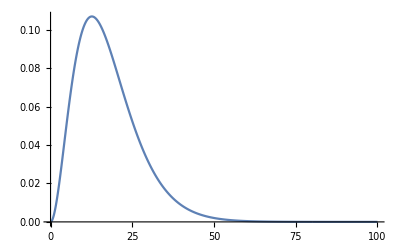

```mathematica
ListPlot[dssBorneCH,Joined->True]
```

```mathematica
InterpolateCorrection=Interpolation[dssBorneCH]
```

InterpolatingFunction[{{0.001, 99.991}}, <>]

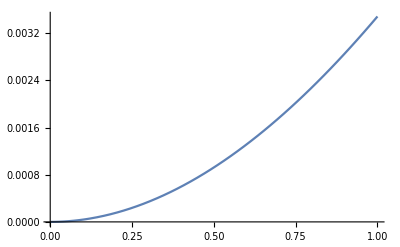

```mathematica
Plot[InterpolateCorrection[x],{x,0.001,1}]
```

```mathematica
InterpolateDensity=Interpolation[dssBorneH]
InterpolateCorrection=Interpolation[dssBorneCH]
```

InterpolatingFunction[{{0.001, 99.991}}, <>]

InterpolatingFunction[{{0.001, 99.991}}, <>]

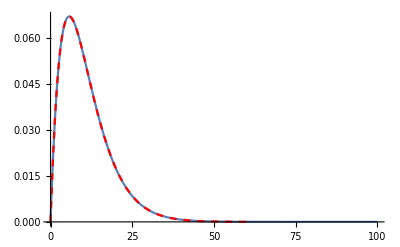

```mathematica
Show[Plot[-InterpolateDensity'[x],{x,0.001,100}],Plot[D[1-Finf[s,1],s]/.s->x,{x,0,60},PlotStyle->{Red,Dashed}]]
```

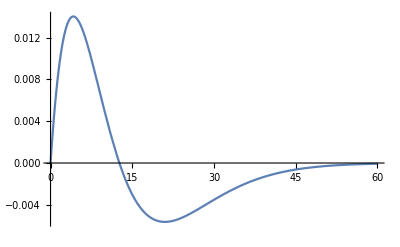

```mathematica
Plot[InterpolateCorrection'[x],{x,0.001,60}]
```

### Differential Equation Approach

```mathematica
aval=1;
Acoef[x_,a_]:=4x^2*D[UInf[x,a],{x,2}]
Bcoef[x_,a_]:=24x*D[UInf[x,a],{x,1}]^2-16UInf[x,a]D[UInf[x,a],{x,1}]+4(x-a^2)D[UInf[x,a],x]-2UInf[x,a]
Ccoef[x_,a_]:=-2D[UInf[x,a],x](4D[UInf[x,a],x]+1)
Dcoef[x_,a_]:=1/8(x D[UInf[x,a],x]-UInf[x,a])^2
rho1[x_,a_]:=-1/192((a^2+2x)BesselJ[a,Sqrt[x]]^2+x BesselJP[a,Sqrt[x]]^2+4Sqrt[x]BesselJ[a,Sqrt[x]]BesselJP[a,Sqrt[x]])
```

```mathematica
rho1IC1=-Limit[x^(-aval)*rho1[x,aval],x->0]
rho1IC2=-Limit[D[x^(-aval)*rho1[x,aval],x],x->0]
```

#### Known formulas

```mathematica
M[x_,a_]:=Table[BesselI[Abs[i-j],x],{i,a},{j,a}]
m[x_,a_]:=Table[BesselI[Abs[2+i-j],x],{i,a},{j,a}]
m1[x_,a_]:=Table[BesselI[Abs[4+i-j],x],{i,a},{j,a}]
Finf[x_,a_]:=Exp[-x/4]*Det[M[Sqrt[x],a]]
finf[x_,a_]:=1/2 Exp[-x/4]*Det[m[Sqrt[x],a]]
f1inf1[x_,a_]:=1/4 Exp[-x/4]*Det[m1[Sqrt[x],a]]
```

#### Power Series Solution

```mathematica
power=100;
sigma1[x_,a_]:=Sum[c[p]x^p,{p,a+1,power}];
```

```mathematica
sigmaCoeff=NSolve[Table[SeriesCoefficient[Acoef[x,aval]*D[sigma1[x,aval],{x,2}]+Bcoef[x,aval]*D[sigma1[x,aval],x]+Ccoef[x,aval]*sigma1[x,aval]-Dcoef[x,aval],{x,0,n}]==0,{n,0,power}]/.{c[aval+1]->rho1IC1,c[aval+2]->rho1IC2},Table[c[p],{p,aval+3,power}],WorkingPrecision->500][[1]];
```

```mathematica
CorrectDE[x_]:=CorrectDE[x]=Integrate[sigma1[s,aval]/s/.{c[aval+1]->rho1IC1,c[aval+2]->rho1IC2}/.sigmaCoeff,{s,0,x}]
```

```mathematica
ysol=NDSolve[{y''[x]+((2(aval+1))/x+(24x*D[UInf[x,aval],{x,1}]^2-16UInf[x,aval]D[UInf[x,aval],{x,1}]+4(x-aval^2)D[UInf[x,aval],x]-2UInf[x,aval])/(4x^2*D[UInf[x,aval],{x,2}]))y'[x]+((aval(aval+1))/x^2+(aval+1)/x*(24x*D[UInf[x,aval],{x,1}]^2-16UInf[x,aval]D[UInf[x,aval],{x,1}]+4(x-aval^2)D[UInf[x,aval],x]-2UInf[x,aval])/(4x^2*D[UInf[x,aval],{x,2}])+(-2D[UInf[x,aval],x](4D[UInf[x,aval],x]+1))/(4x^2*D[UInf[x,aval],{x,2}]))y[x]-1/x^(aval+1)(1/8(x D[UInf[x,aval],x]-UInf[x,aval])^2)/(4x^2*D[UInf[x,aval],{x,2}])==0
,y[0.0001]==1/128,y'[0.0001]==-1/768},y[x],{x,0.0001,60}]
```

```mathematica
sigma2[x_]:=Evaluate[x^(aval+1)*y[x]/.ysol[[1]]]
Plot[Finf[x,aval]*Evaluate[NIntegrate[sigma2[s]/s,{s,0,x}]],{x,0.0001,60}]
```

```mathematica
Show[Plot[D[Finf[y,aval],y]*Evaluate[NIntegrate[sigma2[s]/s,{s,0,x}]]+Finf[x,aval]*sigma2[x]/x/.y->x,{x,0.0001,60}],Plot[InterpolateCorrection'[x],{x,0,80},PlotStyle->{Red,Dashed}]]
```

### Correction Numerics

```mathematica
HardEdgePDFN20a1Loop1=Import["C:/Users/aktrinh/Documents/Research/Hard edge corrections/Matlab/LaguerreSmallEig_N20_a1Trials1000000000Loop1.csv"];
HardEdgePDFN20a1Loop2=Import["C:/Users/aktrinh/Documents/Research/Hard edge corrections/Matlab/LaguerreSmallEig_N20_a1Trials1000000000Loop2.csv"];
HardEdgePDFN20a1Loop3=Import["C:/Users/aktrinh/Documents/Research/Hard edge corrections/Matlab/LaguerreSmallEig_N20_a1Trials1000000000Loop3.csv"];
HardEdgePDFN20a1Loop4=Import["C:/Users/aktrinh/Documents/Research/Hard edge corrections/Matlab/LaguerreSmallEig_N20_a1Trials1000000000Loop4.csv"];
HardEdgePDFN20a1Loop5=Import["C:/Users/aktrinh/Documents/Research/Hard edge corrections/Matlab/LaguerreSmallEig_N20_a1Trials1000000000Loop5.csv"];
HardEdgePDFN20a1Loop6=Import["C:/Users/aktrinh/Documents/Research/Hard edge corrections/Matlab/LaguerreSmallEig_N20_a1Trials1000000000Loop6.csv"];
HardEdgePDFN20a1Loop7=Import["C:/Users/aktrinh/Documents/Research/Hard edge corrections/Matlab/LaguerreSmallEig_N20_a1Trials1000000000Loop7.csv"];
HardEdgePDFN20a1Loop8=Import["C:/Users/aktrinh/Documents/Research/Hard edge corrections/Matlab/LaguerreSmallEig_N20_a1Trials1000000000Loop8.csv"];
HardEdgePDFN20a1Loop9=Import["C:/Users/aktrinh/Documents/Research/Hard edge corrections/Matlab/LaguerreSmallEig_N20_a1Trials1000000000Loop9.csv"];
HardEdgePDFN20a1Loop10=Import["C:/Users/aktrinh/Documents/Research/Hard edge corrections/Matlab/LaguerreSmallEig_N20_a1Trials1000000000Loop10.csv"];
```

```mathematica
HardEdgePDFN20a1Loop1Interpolate=Interpolation[HardEdgePDFN20a1Loop1];
HardEdgePDFN20a1Loop2Interpolate=Interpolation[HardEdgePDFN20a1Loop2];
HardEdgePDFN20a1Loop3Interpolate=Interpolation[HardEdgePDFN20a1Loop3];
HardEdgePDFN20a1Loop4Interpolate=Interpolation[HardEdgePDFN20a1Loop4];
HardEdgePDFN20a1Loop5Interpolate=Interpolation[HardEdgePDFN20a1Loop5];
HardEdgePDFN20a1Loop6Interpolate=Interpolation[HardEdgePDFN20a1Loop6];
HardEdgePDFN20a1Loop7Interpolate=Interpolation[HardEdgePDFN20a1Loop7];
HardEdgePDFN20a1Loop8Interpolate=Interpolation[HardEdgePDFN20a1Loop8];
HardEdgePDFN20a1Loop9Interpolate=Interpolation[HardEdgePDFN20a1Loop9];
HardEdgePDFN20a1Loop10Interpolate=Interpolation[HardEdgePDFN20a1Loop10];
```

```mathematica
xN20a1=Table[0.05+(p-1)*0.1,{p,1,800}];
```

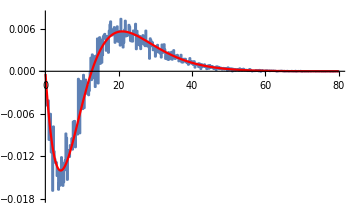

```mathematica
Show[ListStepPlot[Table[{xN20a1[[p]],400*(InterpolateDensity'[xN20a1[[p]]]+(HardEdgePDFN20a1Loop1Interpolate[xN20a1[[p]]]+HardEdgePDFN20a1Loop2Interpolate[xN20a1[[p]]]+HardEdgePDFN20a1Loop3Interpolate[xN20a1[[p]]]+HardEdgePDFN20a1Loop4Interpolate[xN20a1[[p]]]+HardEdgePDFN20a1Loop5Interpolate[xN20a1[[p]]]+HardEdgePDFN20a1Loop6Interpolate[xN20a1[[p]]]+HardEdgePDFN20a1Loop7Interpolate[xN20a1[[p]]]+HardEdgePDFN20a1Loop8Interpolate[xN20a1[[p]]]+HardEdgePDFN20a1Loop9Interpolate[xN20a1[[p]]]+HardEdgePDFN20a1Loop10Interpolate[xN20a1[[p]]])/(10*10^9*0.1))},{p,1,Length[xN20a1]}],PlotRange->{{0,80},{-0.018,0.008}}],Plot[-InterpolateCorrection'[x],{x,0.05,80},PlotStyle->{Red},PlotRange->{-0.018,0.008}]]
```

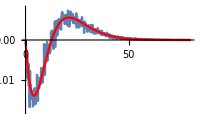
```mathematica
Labeled[
Show[-Graphics-,
PlotRange->All,LabelStyle->Directive[FontSize->12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],ImageSize->{800},TicksStyle->Directive[Black, 20]],
{"N^2[p_N(s/(4N+2a))-p_(∞, 0)(s)]","s"},{Left,Top},RotateLabel->True,LabelStyle->Directive[Bold, 20]]
```

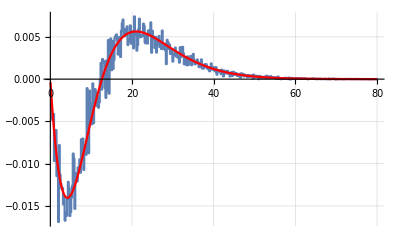
-Graphics-N^2[p_N(s/(4N+2a))-p_(∞, 0)(s)]s

```mathematica
Export["CorrectionNumericsLUE.pdf",
Labeled[
Show[-Graphics-,
PlotRange->All,LabelStyle->Directive[FontSize->12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],ImageSize->{800},TicksStyle->Directive[Black, 20]],
{"N^2[p_N(s/(4N+2a))-p_(∞, 0)(s)]","s"},{Left,Top},RotateLabel->True,LabelStyle->Directive[Bold, 20]]]
```

CorrectionNumericsLUE.pdf